```mathematica
ClearAll["Global`*"]
```

ClearAll::clloc: Cannot clear local variable j.

```mathematica
E2[n_,k_, b_]:= E2[n,k,b]=Sum[ E2[n/j,k-1,b],{j,2,n}]-b Sum[ E2[n/(b j),k-1,b],{j,1,n/b}];E2[n_,0,a_]:=1
D1[n_, k_, b_] := Sum[ Binomial[k+j-1,k-1] b^j 
Sum[FactorialPower[k,a]/a! E2[n/b^j,a,b],{a,0,Log[If[b>2,2,b],n/b^j]}],{j,0,Log[b,n]}]
M2[n_,b_]:=Sum[(-1)^k( E2[n,k,b]-b E2[n/b,k,b]),{k,0,Log[b,n]}]
P[n_,b_]:=Sum[ ((-1)^(k+1) E2[n,k,b]+b^k) /k,{k,1,Log[b,n]}]


EL2[n_, k_,b_ ]:= Sum[ EL2[ n/j,k-1,b],{j,2,n}]-b Sum[ EL2[ n/(j b),k-1,b],{j,1,n/b}]
EL2[n_, 1,b_] :=Sum[ Log[j],{j,2,n}]-b Sum[ Log[j b],{j,1,n/b}]
cheb[n_,b_]:=Sum[ (-1)^(k+1) EL2[n,k,b]+Log[b]b^k,{k,1,Log[b,n]}]
```

```mathematica
N[{M2[100,2],P[100,2],cheb[100,2]}]
```

{1.,28.5333,94.0453}

```mathematica
et[n_, b_,a_] := Binomial[a,4]b^(a-4)Sum[ 1, {j,2,n},{k,2,n/j},{l,2,n/(j k)},{m,2,n/(j k l)}] - Binomial[a,3] b^(a-3) Sum[ 1, {j,2,n},{k,2,n/j},{l,2,n/(j k)},{m,1,n/(j k l b)}]+Binomial[a,2] b^(a-2) Sum[ 1, {j,2,n},{k,2,n/j},{l,1,n/(j k b)},{m,1,n/(j k l b^2)}]-Binomial[a,1] b^(a-1) Sum[ 1, {j,2,n},{k,1,n/(b j)},{l,1,n/(j k b^2)},{m,1,n/(j k l b^3)}]+ Binomial[a,0]b^a Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)},{l,1,n/(j k b^3)},{m,1,n/(j k l b^4)}]
```

```mathematica
et[30,3/2,4]
```

-481/16

```mathematica
E2[30,4,3/2]
```

-481/16

```mathematica
es[n_, b_,a_] := Binomial[a,2] b^(a-2) Sum[ 1, {j,2,n},{k,2,n/j}]-Binomial[a,1] b^(a-1) Sum[ 1, {j,2,n},{k,1,n/(b j)}]+ Binomial[a,0]b^a Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}]
es3[n_, b_,a_] := -3 b^1 Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)}]+3 b^2 Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}]- 1b^3 Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}]
es4[n_, b_,a_] := 6 b^2 Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)}]-
4 b^3 Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}]+ 1b^4 Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}]
es5[n_, b_,a_] := -10 b^3 Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)},{s,1,n/(j k m l b^3)}]+5 b^4 Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}, {s,1,n/(l j k m b^4)}]- 1b^5 Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}, {s,1,n/(j k m l b^5)}]


esa[n_, b_,a_] := {Binomial[a,2] b^(a-2) Sum[ 1, {j,2,n},{k,2,n/j}],-Binomial[a,1] b^(a-1) Sum[ 1, {j,2,n},{k,1,n/(b j)}],+ Binomial[a,0]b^a Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}]}
es3a[n_, b_] := {-3 b^1 Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)}],3 b^2 Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}],- 1b^3 Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}]}
es4a[n_, b_] := {6 b^2 Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)}],-4 b^3 Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}], 1b^4 Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}]}
es5a[n_, b_,a_] := {-10 b^3 Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)},{s,1,n/(j k m l b^3)}],5 b^4 Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}, {s,1,n/(l j k m b^4)}],- 1b^5 Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}, {s,1,n/(j k m l b^5)}]}

es2a2[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j}],Sum[ 1, {j,2,n},{k,1,n/(b j)}],Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}]}
es3a2[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)}],Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}],Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}]}
es4a2[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)}],Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}], Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}]}
es5a2[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)},{s,1,n/(j k m l b^3)}],Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}, {s,1,n/(l j k m b^4)}],Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}, {s,1,n/(j k m l b^5)}]}
```

```mathematica
es[10,3/2,2]
```

2

```mathematica
E2[10,2,3/2]
```

2

```mathematica
es3[6,3/2,3]
```

-9/8

```mathematica
E2[6,3,3/2]
```

-9/8

```mathematica
es4[6,3/2,4]
```

81/16

```mathematica
E2[6,4,3/2]
```

81/16

```mathematica
N[es2a2[6,1.1,2]]
```

```mathematica
es2a2[6.,1.0000001]
```

{3,5,10}

```mathematica
N[es3a2[6,1.000001]]
```

{1.,6.,16.}

```mathematica
N[es4a2[6,1.000001]]
```

{1.,7.,23.}

```mathematica
es5a2[6,1.000001,2]
```

{1,8,31}

```mathematica
Binomial[p,0]
```

1

```mathematica
es5a[n_, b_,a_] := {-10 b^3 Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)},{s,1,n/(j k m l b^3)}],5 b^4 Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}, {s,1,n/(l j k m b^4)}],- 1b^5 Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}, {s,1,n/(j k m l b^5)}]}

es2a2[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j}],Sum[ 1, {j,2,n},{k,1,n/(b j)}],Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}]}
es3a2[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)}],Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}],Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}]}
es4a2[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)}],Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}], Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}]}
es5a2[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)},{s,1,n/(j k m l b^3)}],Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}, {s,1,n/(l j k m b^4)}],Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}, {s,1,n/(j k m l b^5)}]}

ff[n_, k_, b_,r_] := Sum[ ff[n/( j b), k-1, b,r],{j,1,n}];ff[n_, 0, b_,r_] :=1

es5a3[n_, b_] := {Sum[ 1, {j,2,n},{k,2,n/j},{m,1,n/(j k b)},{l,1,n/(j k m b^2)},{s,1,n/(j k m l b^3)}],Sum[ 1, {j,2,n},{k,1,n/(b j)}, {m,1,n/( j k b^2)}, {l,1,n/(j k m b^3)}, {s,1,n/(l j k m b^4)}],Sum[ 1, {j,1,n/b},{k,1,n/(b^2 j)}, {m, 1, n/(j k b^3)}, {l,1,n/(j k m b^4)}, {s,1,n/(j k m l b^5)}]}

esp[n_, b_,p_] := {Sum[ ff[n/(j k),p,b,1], {j,2,n},{k,2,n/j}],Sum[ ff[n/j,p+1,b,1], {j,2,n}],ff[n,p+2,b,1]}
esp2[n_, p_, b_] := (-1)^p(b^(p-2)Binomial[p,2]Sum[ ff[n/(j k),p-2,b,1], {j,2,n},{k,2,n/j}]-b^(p-1)Binomial[p,1]Sum[ ff[n/j,p-1,b,1], {j,2,n}]+b^p Binomial[p,0]ff[n,p,b,1])

esp3[n_, p_, b_] := (-1)^p(b^(p-2)Binomial[p,2]-b^(p-1)Binomial[p,1]Sum[ ff[n/j,p-1,b,1], {j,2,n}]+b^p Binomial[p,0]ff[n,p,b,1])
esp3a[n_, p_, b_] := {b^(p-2)Binomial[p,2],-b^(p-1)Binomial[p,1]Sum[ ff[n/j,p-1,b,1], {j,2,n}],b^p Binomial[p,0]ff[n,p,b,1]}
esp3b[n_, p_, b_] := {b^(p-2)((p-1)(p)/2),-b^(p-1)((p+1)(p+2)-2),b^p ((p+4)(p+3)/2-5)}
esp3ab[n_, p_, b_] := {-b^(p-1)Binomial[p,1]Sum[ ff[n/j,p-1,b,1], {j,2,n}],b^p Binomial[p,0]ff[n,p,b,1],-b^(p-1)((p+1)(p+2)-2),b^p ((p+4)(p+3)/2-5)}
esp3a2[n_, p_, b_] := {b^(p-2)((p)(p-1)/2),-b^(p-1)p Sum[ ff[n/j,p-1,b,1], {j,2,n}],b^p ff[n,p,b,1]}
esp3c[n_, p_, b_] := (-1)^(p)(b^(p-2)((p-1)(p)/2)-b^(p-1)((p+1)(p+2)-2)+b^p ((p+4)(p+3)/2-5))

Table[esp3a2[6,n,1.01],{n,1,30}]//TableForm
```

0. | -5. | 6.06
1. | -16.16 | 10.201
3.03 | -18.3618 | 16.4848
6.1206 | -28.8484 | 23.9339
10.303 | -41.6242 | 32.5813
15.6091 | -56.7545 | 42.4608
22.0712 | -74.3064 | 53.6068
29.7226 | -94.3479 | 66.0543
38.5969 | -116.949 | 79.839
48.7286 | -142.179 | 94.9975
60.1527 | -170.112 | 111.567
72.9051 | -200.82 | 129.585
87.0221 | -234.38 | 149.09
102.541 | -270.866 | 170.122
119.5 | -310.358 | 192.721
137.937 | -352.935 | 216.927
157.892 | -398.677 | 242.782
179.405 | -447.667 | 270.329
202.516 | -499.99 | 299.611
227.268 | -555.73 | 306.268
253.703 | -589.352 | 337.675
281.864 | -650.703 | 370.925
311.795 | -715.712 | 406.064
343.542 | -784.47 | 443.137
377.149 | -857.071 | 482.194
412.664 | -933.61 | 523.284
450.134 | -1014.19 | 566.454
489.607 | -1098.9 | 611.758
531.133 | -1187.84 | 659.245
574.762 | -1281.12 | 708.969

```mathematica
esp3a[6,5,1.00001]
```

{10.0003,-40.0016,31.0016,40,31}

```mathematica
esp3b[6,5,1.00001]
```

{10.0003,-40.0016,31.0016}

```mathematica
Binomial[5,2]
```

10

```mathematica
Binomial[p,2]
```

1/2 (-1+p) p

```mathematica
es5a3[6,1.000001]
```

{1,8,31}

```mathematica
esp[6,1.000001,3]
```

{1,8,31}

```mathematica
N[es4a2[6,1.000001]]
```

{1.,7.,23.}

```mathematica
FullSimplify[Expand[b^(p-2)((p-1)(p)/2)-b^(p-1)((p+1)(p+2)-2)+b^p ((p+4)(p+3)/2-5)]]
```

1/2 b^(-2+p) ((-1+p) p-2 b p (3+p)+b^2 (2+p (7+p)))

```mathematica
esp3c[n_, p_, b_] := (-1)^(p)(b^(p-2)((p-1)(p)/2)-b^(p-1)((p+1)(p+2)-2)+b^p ((p+4)(p+3)/2-5))
esp3d[n_, p_, b_] := (-1)^(p)(b^(p-2)((p-1)(p)/2)-b^(p-1)((p+1)(p+2)-2)+b^p ((p+4)(p+3)/2-5))
```

```mathematica
Table[ {1.01^n,esp3[6,n,1.01],esp3c[6,n,aa=1.01], esp3d[6,n,aa=1.01], E2[6, n, aa]},{n,3,30}]//TableForm
```

1.0303 | -1.15302 | -1.15302 | -1.15302 | -1.15302
1.0406 | 1.20606 | 1.20606 | 1.20606 | 1.20606
1.05101 | -1.26016 | -1.26016 | -1.26016 | -1.26016
1.06152 | 1.31532 | 1.31532 | 1.31532 | 1.31532
1.07214 | -1.37157 | -1.37157 | -1.37157 | -1.37157
1.08286 | 1.42891 | 1.42891 | 1.42891 | 1.42891
1.09369 | -1.48737 | -1.48737 | -1.48737 | -1.48737
1.10462 | 1.54697 | 1.54697 | 1.54697 | 1.54697
1.11567 | -1.60772 | -1.60772 | -1.60772 | -1.60772
1.12683 | 1.66964 | 1.66964 | 1.66964 | 1.66964
1.13809 | -1.73274 | -1.73274 | -1.73274 | -1.73274
1.14947 | 1.79706 | 1.79706 | 1.79706 | 1.79706
1.16097 | -1.8626 | -1.8626 | -1.8626 | -1.8626
1.17258 | 1.92939 | 1.92939 | 1.92939 | 1.92939
1.1843 | -1.99745 | -1.99745 | -1.99745 | -1.99745
1.19615 | 2.06679 | 2.06679 | 2.06679 | 2.06679
1.20811 | -2.13743 | -2.13743 | -2.13743 | 20.8166
1.22019 | -22.1944 | 2.2094 | 2.2094 | 1.96778
1.23239 | -2.02648 | -2.28272 | -2.28272 | -2.02648
1.24472 | 2.08628 | 2.35741 | 2.35741 | 2.08628
1.25716 | -2.1472 | -2.43348 | -2.43348 | -2.1472
1.26973 | 2.20925 | 2.51097 | 2.51097 | 2.20925
1.28243 | -2.27245 | -2.58988 | -2.58988 | -2.27245
1.29526 | 2.33682 | 2.67025 | 2.67025 | 2.33682
1.30821 | -2.40238 | -2.7521 | -2.7521 | -2.40238
1.32129 | 2.46915 | 2.83545 | 2.83545 | 2.46915
1.3345 | -2.53714 | -2.92031 | -2.92031 | -2.53714
1.34785 | 2.60638 | 3.00673 | 3.00673 | 2.60638

-1.00003

```mathematica
Table[ {esp3[6,n,1.00001],(esp2[6,n,1.00001]), E2[6,n,1.00001]},{n,1,10}]//TableForm
```

$RecursionLimit::reclim: Recursion depth of 10000 exceeded.

-1.00006 | -1.00006 | -0.00005
-4.99996 | -2.99996 | 3.0001
-1.00015 | -7.00021 | -1.00015
1.0002 | 1.0002 | 1.0002
-1.00025 | -1.00025 | -1.00025
1.0003 | 1.0003 | 1.0003
-1.00035 | -1.00035 | -1.00035
1.0004 | 1.0004 | 1.0004
-1.00045 | -1.00045 | -1.00045
1.0005 | 1.0005 | 1.0005

```mathematica
E2[6,13,1.000001]
```

-1.00007

```mathematica
esp3[6,13, 1.000001]
```

-1.00007

```mathematica
$RecursionLimit=10000
```

10000

DiscretePlot::iterb: Iterator {k, 1, Log[b, n]} does not have appropriate bounds.

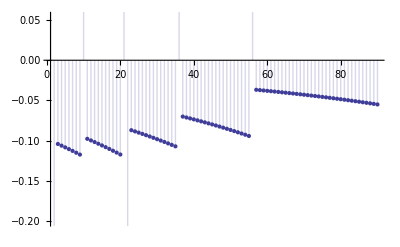

```mathematica
DiscretePlot[ ((-1)^(k+1) E2[n,k,b]+1) /k,{k,1,Log[b,n]}]/.{b->1.02, n->6}
```

```mathematica
esp3c[n_, p_, b_] := (-1)^(p)(b^(p-2)((p-1)(p)/2)-b^(p-1)((p+1)(p+2)-2)+b^p ((p+4)(p+3)/2-5))
```

```mathematica
Sum[ ((-1)^(n-1)esp3c[6,n,1.00001]+1)/n,{n,1,Log[1.00001,1.2]}]
```

-1.00036

```mathematica
FullSimplify[Sum[ ((-1)^(n-1)esp3c[6,n,b]+1)/n,{n,1,Log[b,6/5]}]]
```

1/10 (-7+10 HarmonicNumber[Log[6/5]/Log[b]]+12 b LerchPhi[b,1,Log[(6 b)/5]/Log[b]]+10 Log[1-b]-(6 (-1+b) Log[6/5])/(b Log[b]))

```mathematica
Limit[ 1/10 (-7+10 HarmonicNumber[Log[6/5]/Log[b]]+10 Log[1-b]-(6 (-1+b) Log[6/5])/(b Log[b])),b->1]
```

```mathematica
-7/10+EulerGamma+ⅈ π-3/5 Log[6/5]+Log[Log[6/5]]+Limit[6/5 b LerchPhi[b,1,Log[(6 b)/5]/Log[b]],b->1]
```

-7/10+EulerGamma+ⅈ π+Limit[6/5 b LerchPhi[b,1,Log[(6 b)/5]/Log[b]],b→1]-3/5 Log[6/5]+Log[Log[6/5]]

```mathematica
Limit[1/10 (12 b LerchPhi[b,1,Log[(6 b)/5]/Log[b]]),b->1]
```

Limit[6/5 b LerchPhi[b,1,Log[(6 b)/5]/Log[b]],b→1]

```mathematica
fe[b_]:=-7/10+EulerGamma+ⅈ π+6/5 b LerchPhi[b,1,Log[(6 b)/5]/Log[b]]-3/5 Log[6/5]+Log[Log[6/5]]
```

```mathematica
fe[1.00000001]
```

-1.00037-2.33621×10^-9 ⅈ

```mathematica
FullSimplify[Sum[ ((-1)^(n-1)esp3c[6,n,b]+1)/n,{n,1,Log[b,6/4]}]-Sum[ ((-1)^(n-1)esp3c[6,n,b]+1)/n,{n,1,Log[b,6/5]}]]
```

1/20 (-21-20 HarmonicNumber[Log[6/5]/Log[b]]+20 HarmonicNumber[Log[3/2]/Log[b]]-24 b LerchPhi[b,1,Log[(6 b)/5]/Log[b]]+30 b LerchPhi[b,1,Log[(3 b)/2]/Log[b]]-(3 (-1+b) Log[1875/512])/(b Log[b]))

```mathematica
Limit[1/20 (-21-20 HarmonicNumber[Log[6/5]/Log[b]]+20 HarmonicNumber[Log[3/2]/Log[b]]-(3 (-1+b) Log[1875/512])/(b Log[b])),b->1]
```

-21/20-3/20 Log[1875/512]-Log[Log[6/5]]+Log[Log[3/2]]